```mathematica
2-2
```

0

```mathematica
({{Subscript[a, 1], Subscript[a, 2]}, {Subscript[b, 1], Subscript[b, 2]}})
```

{{a_1,a_2},{b_1,b_2}}

### Construction & application of a Random Transition Matrix

The elements of such a matrix are "transition probabilities." Writing

```mathematica
𝕋=({{Subscript[T, 1,1], Subscript[T, 1,2], Subscript[T, 1,3], Subscript[T, 1,4]}, {Subscript[T, 2,1], Subscript[T, 2,2], Subscript[T, 2,3], Subscript[T, 2,4]}, {Subscript[T, 3,1], Subscript[T, 3,2], Subscript[T, 3,3], Subscript[T, 3,4]}, {Subscript[T, 4,1], Subscript[T, 4,2], Subscript[T, 4,3], Subscript[T, 4,4]}});
```

we understand

T_(j,k)=probability of transition j←k  from site k to site j

(p_1[n+1]
p_2[n+1]
p_3[n+1]
p_4[n+1])=𝕋.(p_1[n]
p_2[n]
p_3[n]
p_4[n])

where

p_k[n]= probability that the "walker"is at site k after n steps

Necessarily, the elements on any row must sum to unity:

∑_(j=1)^N p_(j,k)=1

To construct a random instance of such a matrix (in the case N = 5) I construct a square array of numbers all of which (in this instance) fall randomly on the interval [0, 1]:

```mathematica
RowData=Table[Table[RandomReal[],{j,1,5}],{k,1,5}]
```

{{0.0874177,0.0922823,0.117978,0.989378,0.383611},{0.929903,0.135377,0.760577,0.0180194,0.655447},{0.283288,0.478153,0.348527,0.29897,0.157543},{0.466832,0.182819,0.782057,0.527222,0.463428},{0.126038,0.0392415,0.626032,0.754721,0.739626}}

Normalizing so that the elements on each row sum to unity, I construct the random transition matrix

```mathematica
𝕋=Transpose[Table[RowData⟦k⟧/Total[RowData⟦k⟧],{k,1,5}]]
```

{{0.052325,0.372062,0.180844,0.192718,0.055143},{0.0552368,0.0541654,0.30524,0.0754713,0.0171686},{0.0706175,0.304313,0.22249,0.322849,0.273896},{0.592205,0.0072097,0.190855,0.217648,0.330198},{0.229616,0.26225,0.100571,0.191313,0.323594}}

and check that the elements of each column do in fact sum to unity:

```mathematica
Table[Total[Transpose[𝕋]⟦k⟧],{k,1,5}]
```

{1.,1.,1.,1.,1.}

```mathematica
𝕋//MatrixForm
```

(0.052325 | 0.372062 | 0.180844 | 0.192718 | 0.055143
0.0552368 | 0.0541654 | 0.30524 | 0.0754713 | 0.0171686
0.0706175 | 0.304313 | 0.22249 | 0.322849 | 0.273896
0.592205 | 0.0072097 | 0.190855 | 0.217648 | 0.330198
0.229616 | 0.26225 | 0.100571 | 0.191313 | 0.323594)

Random walks are deterministic processes, so we expect them to be reversible. Introducing

```mathematica
𝕌=Inverse[𝕋];
```

```mathematica
𝕌//MatrixForm
```

(2.28489 | -0.830704 | -2.22092 | 2.04192 | -0.549055
2.91038 | -0.0246647 | -2.73931 | -1.05137 | 2.89678
-0.95438 | 4.41402 | -0.737489 | -0.75076 | 1.31875
1.08236 | -4.39406 | 6.53782 | 2.74891 | -8.29005
-4.32325 | 1.83541 | 0.159896 | -1.9887 | 5.62358)

we see that many of the elements of the inverted transition matrix cannot be interpreted as "transition probabilities," (some fall outside the interval [0, 1], some even wear negative signs) though they do—for non-obvious reasons—conform to one of the characteristic features of transition matrices: the elements of each column sum to unity:

```mathematica
Table[Total[Transpose[𝕌]⟦k⟧],{k,1,5}]
```

{1.,1.,1.,1.,1.}

Looking to the eigenvalues of 𝕋

```mathematica
λ[k_]:=Eigenvalues[𝕋]⟦k⟧
```

```mathematica
Table[{k,λ[k]},{k,1,5}]//TableForm
```

1 | 1.
2 | -0.322641
3 | 0.0465696+0.212553 ⅈ
4 | 0.0465696-0.212553 ⅈ
5 | 0.0997257

which Mathematica presents in order of descending norm

```mathematica
Table[Norm[λ[k]],{k,1,5}]
```

{1.,0.322641,0.217595,0.217595,0.0997257}

of which one is very much larger than the others. We observe that some eigenvalues are real, some complex, and that the complex eigenvalues occur in conjugate pairs. Those reality/complixity/conjugacy distinctions are repeated when one looks to the corresponding eigenvectors:

```mathematica
v[k_]:=Transpose[{Eigenvectors[𝕋]⟦k⟧}]
```

```mathematica
Table[{k,MatrixForm[v[k]]},{k,1,5}]//TableForm
```

1 | (-0.341675
-0.245075
-0.52829
-0.581378
-0.453989)
2 | (-0.422875
0.314704
-0.477554
0.694449
-0.108724)
3 | (0.27281-0.313792 ⅈ
0.471395-0.0200694 ⅈ
0.118096+0.388619 ⅈ
-0.61107+0. ⅈ
-0.251231-0.0547578 ⅈ)
4 | (0.27281+0.313792 ⅈ
0.471395+0.0200694 ⅈ
0.118096-0.388619 ⅈ
-0.61107+0. ⅈ
-0.251231+0.0547578 ⅈ)
5 | (-0.291639
0.116775
0.199253
-0.668438
0.644049)

We check that we do in fact have now in hand 5 solutions of the "eigen-equation:"

```mathematica
Table[Chop[𝕋.v[k]-λ[k]v[k]]//MatrixForm,{k,1,5}]
```

{(0
0
0
0
0),(0
0
0
0
0),(0
0
0
0
0),(0
0
0
0
0),(0
0
0
0
0)}

The eigenvectors are, as supplied by Mathematica, normalized

```mathematica
Table[Norm[v[k]],{k,1,5}]
```

{1.,1.,1.,1.,1.}

but are not orthogonal (we had no reason to expect them to be):

```mathematica
Table[Chop[Conjugate[Transpose[v[j]]].v[k]],{j,1,5},{k,1,5}]//MatrixForm
```

((1.) | (-0.0347308) | (0.19819-0.0683109 ⅈ) | (0.19819+0.0683109 ⅈ) | (0.0619879)
(-0.0347308) | (1.) | (-0.420454-0.053254 ⅈ) | (-0.420454+0.053254 ⅈ) | (-0.469297)
(0.19819+0.0683109 ⅈ) | (-0.420454+0.053254 ⅈ) | (1.) | (0.494217+0.07083 ⅈ) | (0.245674-0.131337 ⅈ)
(0.19819-0.0683109 ⅈ) | (-0.420454-0.053254 ⅈ) | (0.494217-0.07083 ⅈ) | (1.) | (0.245674+0.131337 ⅈ)
(0.0619879) | (-0.469297) | (0.245674+0.131337 ⅈ) | (0.245674-0.131337 ⅈ) | (1.))

It is a curious fact that all eigenvectors except the leading eigenvector have elements that sum to zero:

```mathematica
Table[Chop[Total[Transpose[v[k]]⟦1⟧]],{k,1,5}]
```

{-2.15041,0,0,0,0}

The leading eigenvector is unique in that it can be "unitized," meaning multiplied by a factor so as to cause the elements to sum to unity:

```mathematica
V=v[1]/Total[Transpose[v[1]]⟦1⟧];
```

```mathematica
V//MatrixForm
Total[Transpose[V]⟦1⟧]
```

(0.158889
0.113967
0.24567
0.270357
0.211118)

1.

Notice that V possesses the structure of a probability vector.

```mathematica
𝕋.({{1}, {0}, {0}, {0}, {0}})//MatrixForm
```

(0.052325
0.0552368
0.0706175
0.592205
0.229616)

Generally,

𝕋.(probability vector)=another probability vector

which I illustrate by simple example:

```mathematica
𝕋.({{1}, {0}, {0}, {0}, {0}})//MatrixForm
Total[Transpose[%]⟦1⟧]
```

(0.052325
0.0552368
0.0706175
0.592205
0.229616)

1.

Iteration, whatever the initial probability vector, leads inevitably back to V:

```mathematica
?MatrixPower
```

MatrixPower[m,n] gives the n^th matrix power of the matrix m. 
MatrixPower[m,n,v] gives the n^th matrix power of the matrix m applied to the vector v.

```mathematica
MatrixForm[MatrixPower[𝕋,10].({{1}, {0}, {0}, {0}, {0}})-V]
Total[Transpose[%]⟦1⟧]
```

(3.20231×10^-6
-2.47488×10^-6
3.50276×10^-6
-5.11691×10^-6
8.86717×10^-7)

-1.80411×10^-16

```mathematica
MatrixForm[MatrixPower[𝕋,20].({{1}, {0}, {0}, {0}, {0}})-V]
Total[Transpose[%]⟦1⟧]
```

(3.90374×10^-11
-2.91025×10^-11
4.41095×10^-11
-6.41043×10^-11
1.00593×10^-11)

-4.57967×10^-16

To illustrate the point more generally, I construct a random initial probability vector

```mathematica
x=Table[RandomReal[],{k,1,5}]
```

{0.731929,0.796965,0.101584,0.150977,0.778208}

```mathematica
Subscript[p, 0]=Transpose[{x/Total[x]}];
Subscript[p, 0]//MatrixForm
```

(0.285947
0.311356
0.0396866
0.058983
0.304027)

and obtain

```mathematica
MatrixForm[MatrixPower[𝕋,10].Subscript[p, 0]-V]
Total[Transpose[%]⟦1⟧]
```

(-6.50511×10^-7
4.63308×10^-7
-8.12162×10^-7
1.1449×10^-6
-1.45534×10^-7)

-1.249×10^-16

The process

p_0→→→⋯→V

is deterministic, and reversible-in-principle

```mathematica
MatrixPower[𝕋,-10].MatrixPower[𝕋,10].Subscript[p, 0]-Subscript[p, 0]//MatrixForm
```

(3.92991×10^-8
-2.9546×10^-8
3.24033×10^-8
2.03703×10^-7
-1.61839×10^-7)

but if the number of iterative steps is too large the reversal is sabotaged by numerical imprecision:

```mathematica
MatrixPower[𝕋,-20].MatrixPower[𝕋,20].Subscript[p, 0]-Subscript[p, 0]//MatrixForm
```

(699.581
60.3613
-584.799
1351.23
-1885.24)

```mathematica
Total[Transpose[%]⟦1⟧]
```

-358.871

### Repetition with a higher-dimensional example

```mathematica
BigRowData = Table[Table[RandomReal[], {j, 1, 10}], {k, 1, 10}];
```

```mathematica
𝕋𝕋=Transpose[Table[BigRowData⟦k⟧/Total[BigRowData⟦k⟧],{k,1,10}]];
```

```mathematica
Table[Total[Transpose[𝕋𝕋]⟦k⟧],{k,1,10}]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
λλ[k_]:=Eigenvalues[𝕋𝕋]⟦k⟧
```

```mathematica
Table[{k,λλ[k]},{k,1,10}]//TableForm
```

1 | 1.
2 | -0.240152
3 | 0.22544
4 | -0.112824+0.019648 ⅈ
5 | -0.112824-0.019648 ⅈ
6 | 0.102259+0.0250033 ⅈ
7 | 0.102259-0.0250033 ⅈ
8 | -0.019761+0.0611203 ⅈ
9 | -0.019761-0.0611203 ⅈ
10 | 0.023632

```mathematica
Table[Norm[λλ[k]],{k,1,10}]
```

{1.,0.240152,0.22544,0.114522,0.114522,0.105272,0.105272,0.0642354,0.0642354,0.023632}

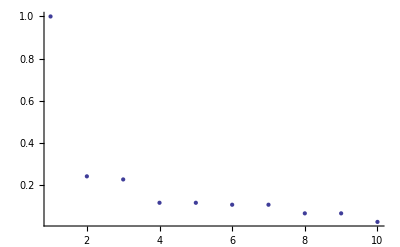

```mathematica
ListPlot[%]
```

Notice that again, one of the norms is very much larger than  the others.

```mathematica
vv[k_]:=Transpose[{Eigenvectors[𝕋𝕋]⟦k⟧}]
```

```mathematica
Table[Chop[𝕋𝕋.vv[k]-λλ[k]vv[k]]//MatrixForm,{k,1,10}]
```

{(0
0
0
0
0
0
0
0
0
0),(0
0
0
0
0
0
0
0
0
0),(0
0
0
0
0
0
0
0
0
0),(0
0
0
0
0
0
0
0
0
0),(0
0
0
0
0
0
0
0
0
0),(0
0
0
0
0
0
0
0
0
0),(0
0
0
0
0
0
0
0
0
0),(0
0
0
0
0
0
0
0
0
0),(0
0
0
0
0
0
0
0
0
0),(0
0
0
0
0
0
0
0
0
0)}

```mathematica
Table[Norm[vv[k]],{k,1,10}]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
Table[Chop[Total[Transpose[vv[k]]⟦1⟧]],{k,1,10}]
```

{-3.10971,0,0,0,0,0,0,0,0,0}

```mathematica
VV=vv[1]/Total[Transpose[vv[1]]⟦1⟧];
VV//MatrixForm
Total[Transpose[VV]⟦1⟧]
```

(0.105737
0.0909448
0.0884888
0.085466
0.0967041
0.0938527
0.0966088
0.143964
0.0772489
0.120985)

1.

```mathematica
xx=Table[RandomReal[],{k,1,10}];
Subscript[pp, 0]=Transpose[{xx/Total[xx]}];
Subscript[pp, 0]//MatrixForm
Total[Transpose[Subscript[pp, 0]]⟦1⟧]
```

(0.100629
0.14296
0.111055
0.105708
0.153093
0.101835
0.0986622
0.0721127
0.026764
0.0871816)

1.

I demonstrate convergence to VV as the number of iterations increases

```mathematica
Table[{2k,MatrixForm[MatrixPower[𝕋𝕋,2k].Subscript[pp, 0]-VV]},{k,1,8}]//TableForm
```

2 | (-0.000838889
0.000180469
0.00275257
-0.00188383
0.000301033
0.000182947
-0.00161424
0.000382731
-0.00115367
0.00169088)
4 | (-0.0000401884
0.0000157253
0.00014988
-0.00010744
-6.49856×10^-6
0.0000266966
-0.0000960083
0.0000351385
-0.0000515598
0.0000742543)
6 | (-2.36955×10^-6
1.1322×10^-6
8.03637×10^-6
-6.36617×10^-6
-7.21996×10^-7
1.85906×10^-6
-5.51232×10^-6
2.63703×10^-6
-2.73871×10^-6
4.04409×10^-6)
8 | (-1.31974×10^-7
7.43524×10^-8
4.45941×10^-7
-3.72112×10^-7
-5.26224×10^-8
1.11878×10^-7
-3.06936×10^-7
1.67006×10^-7
-1.50814×10^-7
2.15281×10^-7)
10 | (-7.17448×10^-9
4.72511×10^-9
2.50274×10^-8
-2.17307×10^-8
-3.47076×10^-9
6.4995×10^-9
-1.70594×10^-8
1.01×10^-8
-8.39219×10^-9
1.14756×10^-8)
12 | (-3.88741×10^-10
2.94326×10^-10
1.41124×10^-9
-1.26744×10^-9
-2.21498×10^-10
3.75028×10^-10
-9.5028×10^-10
6.0263×10^-10
-4.68724×10^-10
6.13459×10^-10)
14 | (-2.11146×10^-11
1.80814×10^-11
7.97874×10^-11
-7.38252×10^-11
-1.38545×10^-11
2.1619×10^-11
-5.30907×10^-11
3.57395×10^-11
-2.62573×10^-11
3.29154×10^-11)
16 | (-1.15095×10^-12
1.09893×10^-12
4.52041×10^-12
-4.2947×10^-12
-8.53942×10^-13
1.24631×10^-12
-2.9747×10^-12
2.11095×10^-12
-1.47493×10^-12
1.77304×10^-12)

and (working at default machine precision) the computational breakdown of reversibility after about 8 iterations:

```mathematica
Table[{2k,MatrixPower[𝕋𝕋,-2k].MatrixPower[𝕋𝕋,2k].Subscript[pp, 0]-Subscript[pp, 0]//MatrixForm},{k,1,8}]//TableForm
```

2 | (5.35683×10^-15
9.10383×10^-15
1.89154×10^-14
6.27276×10^-15
4.55191×10^-15
-1.15324×10^-14
1.76248×10^-15
2.43833×10^-14
3.52808×10^-14
3.75255×10^-14)
4 | (6.08315×10^-11
1.70661×10^-11
1.85607×10^-10
2.04908×10^-11
-6.88172×10^-13
-1.27758×10^-11
-3.1625×10^-12
-1.57255×10^-10
1.01464×10^-10
-8.53159×10^-11)
6 | (-2.02229×10^-9
5.31477×10^-9
-4.42316×10^-9
5.87683×10^-8
-4.89977×10^-8
-7.90382×10^-8
-5.18421×10^-9
1.28245×10^-8
4.74519×10^-9
-2.75755×10^-8)
8 | (0.000212851
0.0000214092
0.000524569
0.000050426
-0.0000717254
-0.000297476
-0.0000159705
-0.000413066
0.000550575
-0.00062142)
10 | (0.713766
0.0707972
1.09091
0.150219
-0.263191
-0.686429
-0.0937784
-0.903416
1.33564
-0.867657)
12 | (1570.3
58.1163
972.689
63.2877
-236.121
-1145.64
-36.5541
-1208.65
280.304
-1796.86)
14 | (351482.
18659.4
1.94243×10^6
118688.
-97133.2
127271.
-138565.
-1.30533×10^6
865580.
-222478.)
16 | (3.5881×10^9
2.94334×10^8
1.01072×10^10
9.43889×10^8
-1.51119×10^9
-2.21292×10^9
-5.31947×10^8
-6.51241×10^9
5.13754×10^9
-9.35103×10^9)

### Imposition of detailed balancing

The transition matrices considered thus far are asymmetric:

p_(j,k)≠p_(k,j)

We now impose the principle that the probability of jumping j→k is the same as the probability of jumping j←k :

p_(j,k)=p_(k,j)

which renders 𝕋 symmetric.

#### Construction technique:

The method I will use to construct symmetric transition matrices is sketched below:

(A_1 | A_2 | A_3 | A_4 | A_5
□ | □ | □ | □ | □
□ | □ | □ | □ | □
□ | □ | □ | □ | □
□ | □ | □ | □ | □): arrange to have ∑A_k=1
(A_1 | A_2 | A_3 | A_4 | A_5
A_2 | B_1 | B_2 | B_3 | B_4
A_3 | □ | □ | □ | □
A_4 | □ | □ | □ | □
A_5 | □ | □ | □ | □): arrange to have A_2+∑B_k=1
(A_1 | A_2 | A_3 | A_4 | A_5
A_2 | B_1 | B_2 | B_3 | B_4
A_3 | B_2 | C_1 | C_2 | C_3
A_4 | B_3 | □ | □ | □
A_5 | B_4 | □ | □ | □): arrange to have A_3+B_2+∑C_k=1
   etc.

I implement the procedure (which will be found to work except when it fails to work, due to the intrusion of minus signs, from which it provides no protection), proceeding on the assumption that matrix elements are generated randomly by flat distribution on the unit interval, and use the implementation to construct an 8-element population of such 5×5 symmetric transition matrices:

```mathematica
a=Table[RandomReal[],{k,1,5}];
b=Table[RandomReal[],{k,1,4}];
c=Table[RandomReal[],{k,1,3}];
d=Table[RandomReal[],{k,1,2}];
e=Table[RandomReal[],{k,1,1}];
Subscript[Row, 1]=a/Total[a];
Subscript[Row, 2]=Join[{Subscript[Row, 1]⟦2⟧},(1-Subscript[Row, 1]⟦2⟧)/Total[b] b];
Subscript[Row, 3]=Join[{Subscript[Row, 1]⟦3⟧,Subscript[Row, 2]⟦3⟧},(1-Subscript[Row, 1]⟦3⟧-Subscript[Row, 2]⟦3⟧)/Total[c] c];
Subscript[Row, 4]=Join[{Subscript[Row, 1]⟦4⟧,Subscript[Row, 2]⟦4⟧,Subscript[Row, 3]⟦4⟧},(1-Subscript[Row, 1]⟦4⟧-Subscript[Row, 2]⟦4⟧-Subscript[Row, 3]⟦4⟧)/Total[d] d];
Subscript[Row, 5]=Join[{Subscript[Row, 1]⟦5⟧,Subscript[Row, 2]⟦5⟧,Subscript[Row, 3]⟦5⟧,Subscript[Row, 4]⟦5⟧},(1-Subscript[Row, 1]⟦5⟧-Subscript[Row, 2]⟦5⟧-Subscript[Row, 3]⟦5⟧-Subscript[Row, 4]⟦5⟧)/Total[e] e];
Subscript[𝕊, 8]={Subscript[Row, 1],Subscript[Row, 2],Subscript[Row, 3],Subscript[Row, 4],Subscript[Row, 5]};
```

```mathematica
Table[{k,MatrixForm[Subscript[𝕊, k]]},{k,1,8}]
```

{{1,(0.231413 | 0.251353 | 0.1133 | 0.221611 | 0.182323
0.251353 | 0.210678 | 0.214031 | 0.15803 | 0.165909
0.1133 | 0.214031 | 0.319249 | 0.0525974 | 0.300823
0.221611 | 0.15803 | 0.0525974 | 0.239566 | 0.328196
0.182323 | 0.165909 | 0.300823 | 0.328196 | 0.0227492)},{2,(0.0265192 | 0.346908 | 0.065773 | 0.181598 | 0.379201
0.346908 | 0.153666 | 0.341188 | 0.123536 | 0.0347013
0.065773 | 0.341188 | 0.0341884 | 0.468254 | 0.0905961
0.181598 | 0.123536 | 0.468254 | 0.0475713 | 0.17904
0.379201 | 0.0347013 | 0.0905961 | 0.17904 | 0.316462)},{3,(0.27781 | 0.152317 | 0.225969 | 0.125877 | 0.218026
0.152317 | 0.397751 | 0.0824232 | 0.12816 | 0.239349
0.225969 | 0.0824232 | 0.205561 | 0.367567 | 0.118479
0.125877 | 0.12816 | 0.367567 | 0.149786 | 0.228609
0.218026 | 0.239349 | 0.118479 | 0.228609 | 0.195536)},{4,(0.248552 | 0.315988 | 0.261997 | 0.102899 | 0.0705638
0.315988 | 0.182577 | 0.0961402 | 0.221524 | 0.183771
0.261997 | 0.0961402 | 0.0841681 | 0.141331 | 0.416364
0.102899 | 0.221524 | 0.141331 | 0.373486 | 0.16076
0.0705638 | 0.183771 | 0.416364 | 0.16076 | 0.168541)},{5,(0.204278 | 0.105702 | 0.248224 | 0.0520603 | 0.389735
0.105702 | 0.179261 | 0.253034 | 0.0524037 | 0.409599
0.248224 | 0.253034 | 0.0646591 | 0.150642 | 0.283442
0.0520603 | 0.0524037 | 0.150642 | 0.322539 | 0.422356
0.389735 | 0.409599 | 0.283442 | 0.422356 | -0.505131)},{6,(0.162234 | 0.289492 | 0.102505 | 0.149084 | 0.296684
0.289492 | 0.126816 | 0.209296 | 0.0819013 | 0.292495
0.102505 | 0.209296 | 0.186121 | 0.291081 | 0.210996
0.149084 | 0.0819013 | 0.291081 | 0.226073 | 0.25186
0.296684 | 0.292495 | 0.210996 | 0.25186 | -0.0520357)},{7,(0.335917 | 0.23049 | 0.00361696 | 0.373911 | 0.0560651
0.23049 | 0.242759 | 0.179169 | 0.154784 | 0.192797
0.00361696 | 0.179169 | 0.358258 | 0.201903 | 0.257053
0.373911 | 0.154784 | 0.201903 | 0.0917854 | 0.177616
0.0560651 | 0.192797 | 0.257053 | 0.177616 | 0.316468)},{8,(0.255566 | 0.237 | 0.285002 | 0.12356 | 0.0988722
0.237 | 0.162507 | 0.331426 | 0.00585663 | 0.263211
0.285002 | 0.331426 | 0.0660515 | 0.152741 | 0.16478
0.12356 | 0.00585663 | 0.152741 | 0.206461 | 0.511382
0.0988722 | 0.263211 | 0.16478 | 0.511382 | -0.0382452)}}

We verify that (as is evident to the eye) each of those matrices is symmetric

```mathematica
Table[Subscript[𝕊, k]==Transpose[Subscript[𝕊, k]],{k,1,8}]
```

{True,True,True,True,True,True,True,True}

and that the rows/columns of each sum to unity:

```mathematica
TableForm[Table[{j,{Table[Total[Subscript[𝕊, j]⟦k⟧],{k,1,5}]}},{j,1,8}]]
```

1 | 1. | 1. | 1. | 1. | 1.
2 | 1. | 1. | 1. | 1. | 1.
3 | 1. | 1. | 1. | 1. | 1.
4 | 1. | 1. | 1. | 1. | 1.
5 | 1. | 1. | 1. | 1. | 1.
6 | 1. | 1. | 1. | 1. | 1.
7 | 1. | 1. | 1. | 1. | 1.
8 | 1. | 1. | 1. | 1. | 1.

Notice, however, that (in this particular sample) 𝕊_5, 𝕊_6 and 𝕊_8 must be discarded because they contain elements that wear minus signs, and therefore do not admit of interpretation as transition probabilities.

#### Eigenvalues

From real symmetry it follows familiarly that all eigenvalues are real.

{{1.,-0.297283,0.263161,0.111853,-0.0540762},{1.,-0.545158,0.336806,-0.309365,0.0961233},{1.,0.324782,-0.236343,0.126255,0.0117508},{1.,-0.370676,0.249374,0.239645,-0.0610188},{1.,-0.901741,0.264206,-0.183161,0.0863018},{1.,-0.331788,0.209475,-0.207544,-0.0209349},{1.,0.443403,-0.238973,0.0861594,0.0545983},{1.,-0.516051,0.364859,-0.21786,0.0213922}}

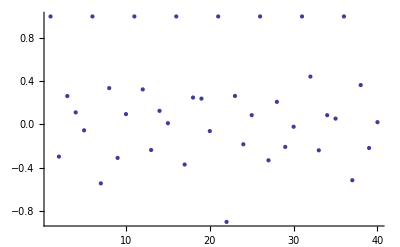

```mathematica
EigenvalueTable=Table[Eigenvalues[Subscript[𝕊, k]],{k,1,8}]
ListPlot[Flatten[EigenvalueTable]]
```

Interestingly, the spectral value 1 is universal,  and all other eigenvalues have absolute value < 1:

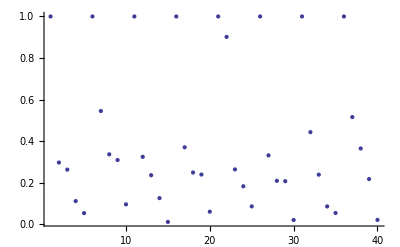

```mathematica
ListPlot[Abs[Flatten[EigenvalueTable]]]
```

#### Eigenvectors

Looking to the respective populations of eigenvectors

```mathematica
Flatten[Table[{j,TableForm[Table[MatrixForm[Transpose[{Eigenvectors[Subscript[𝕊, j]]⟦k⟧}]],{k,1,5}]]},{j,1,8}]]
```

{1,(-0.447214
-0.447214
-0.447214
-0.447214
-0.447214)
(-0.0304899
0.0485206
-0.36596
-0.459384
0.807314)
(-0.32831
0.0615125
0.774209
-0.53681
0.0293979)
(-0.495299
-0.566826
0.172362
0.507492
0.382271)
(-0.667804
0.687438
-0.192262
0.207975
-0.0353469),2,(0.447214
0.447214
0.447214
0.447214
0.447214)
(0.429849
-0.42092
0.616224
-0.489941
-0.135212)
(0.293797
-0.324465
-0.459292
-0.243603
0.733563)
(0.613593
-0.293597
-0.351037
0.470271
-0.43923)
(-0.390406
-0.656772
0.293414
0.528641
0.225123),3,(-0.447214
-0.447214
-0.447214
-0.447214
-0.447214)
(-0.0838007
0.759075
-0.514157
-0.344609
0.183492)
(-0.231806
-0.00375182
0.607914
-0.689849
0.317493)
(0.833467
-0.264106
-0.210917
-0.43107
0.0726257)
(-0.211132
-0.392478
-0.348708
0.139758
0.812561),4,(-0.447214
-0.447214
-0.447214
-0.447214
-0.447214)
(-0.366335
0.296349
0.677558
-0.0446335
-0.562938)
(0.184424
-0.169354
0.420126
-0.794704
0.359509)
(0.653409
0.40651
-0.260198
-0.299045
-0.500675)
(0.452597
-0.719893
0.310977
0.277533
-0.321214),5,(-0.447214
-0.447214
-0.447214
-0.447214
-0.447214)
(0.253901
0.277899
0.0783546
0.271993
-0.882149)
(-0.37379
-0.324212
-0.185557
0.848226
0.0353327)
(0.310175
0.345554
-0.871034
0.0722596
0.143046)
(-0.706828
0.705869
0.026995
-0.0361986
0.010163),6,(-0.447214
-0.447214
-0.447214
-0.447214
-0.447214)
(-0.227493
-0.354456
-0.0114549
-0.27181
0.865214)
(-0.496948
-0.431089
0.438799
0.601679
-0.112441)
(-0.575624
0.567979
-0.471324
0.307325
0.171644)
(-0.412246
0.407336
0.620627
-0.519281
-0.0964352),7,(0.447214
0.447214
0.447214
0.447214
0.447214)
(0.682104
0.0628794
-0.555712
0.22478
-0.414052)
(-0.550624
0.161311
-0.248576
0.769251
-0.131362)
(0.104902
-0.405227
0.633097
0.262919
-0.595691)
(0.14333
-0.778342
-0.169063
0.297659
0.506416),8,(0.447214
0.447214
0.447214
0.447214
0.447214)
(0.0638023
-0.357663
0.10843
-0.554995
0.740425)
(0.413903
0.388055
0.264337
-0.674093
-0.392201)
(-0.275819
-0.396308
0.839817
0.0702827
-0.237974)
(-0.740633
0.603681
0.114349
-0.180663
0.203265)}

we note that the leading eigenvector (the one associated with the leading eigenvalue λ = 1) is the same in every instance, that all of its elements are equal, and that all wear the same sign (which could without loss of generality be taken to be—i.e., adjusted to be—positive). 

The real symmetry of the 𝕊-matrices causes their eigenvectors (which Mathematica delivers in normalized form) to be orthogonal, which we verify:

```mathematica
Table[{n,Table[Chop[{Eigenvectors[Subscript[𝕊, n]]⟦j⟧}.Transpose[{Eigenvectors[Subscript[𝕊, n]]⟦k⟧}]]⟦1⟧⟦1⟧,{j,1,5},{k,1,5}]//TableForm},{n,1,8}]
```

{{1,1. | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0
0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 1.},{2,1. | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0
0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 1.},{3,1. | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0
0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 1.},{4,1. | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0
0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 1.},{5,1. | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0
0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 1.},{6,1. | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0
0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 1.},{7,1. | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0
0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 1.},{8,1. | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0
0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 1.}}

From the fact that the 𝕊-matrices possess the structure peculiar to transition matrices it appears to follow that the elements of all but the leading eigenvectors sum to zero:

```mathematica
Table[Chop[Total[Eigenvectors[Subscript[𝕊, j]]⟦k⟧]],{j,1,8},{k,1,5}]
```

{{-2.23607,0,0,0,0},{2.23607,0,0,0,0},{-2.23607,0,0,0,0},{-2.23607,0,0,0,0},{-2.23607,0,0,0,0},{-2.23607,0,0,0,0},{2.23607,0,0,0,0},{2.23607,0,0,0,0}}

The leading eigenvectors—and only the leading eigenvectors—can be scaled to become "probability vectors:"

```mathematica
V[j_]:=Transpose[{(Eigenvectors[Subscript[𝕊, j]]⟦1⟧)/Total[Eigenvectors[Subscript[𝕊, j]]⟦1⟧]}];
```

```mathematica
Table[MatrixForm[V[j]],{j,1,8}]
```

{(0.2
0.2
0.2
0.2
0.2),(0.2
0.2
0.2
0.2
0.2),(0.2
0.2
0.2
0.2
0.2),(0.2
0.2
0.2
0.2
0.2),(0.2
0.2
0.2
0.2
0.2),(0.2
0.2
0.2
0.2
0.2),(0.2
0.2
0.2
0.2
0.2),(0.2
0.2
0.2
0.2
0.2)}

Those vectors—the same in every instance—refer to a flat or "equal likelyhood" distribution, an "equipartition of probability." Interestingly, these results hold even when occasional minus signs intrude into the structure of 𝕊.

#### Interation and its asymptotic endstate

```mathematica
Subscript[𝕊, 1].({{1}, {0}, {0}, {0}, {0}})//MatrixForm
```

(0.231413
0.251353
0.1133
0.221611
0.182323)

```mathematica
Table[MatrixForm[MatrixPower[Subscript[𝕊, 1],n].({{1}, {0}, {0}, {0}, {0}})],{n,0,10}]
```

{(1.
0.
0.
0.
0.),(0.231413
0.251353
0.1133
0.221611
0.182323),(0.21192
0.200641
0.18269
0.209892
0.194856),(0.202213
0.200136
0.194935
0.202514
0.200202),(0.200566
0.199932
0.198856
0.200914
0.199732),(0.200138
0.199983
0.199652
0.200186
0.200042),(0.200037
0.199993
0.199923
0.200068
0.199979),(0.200009
0.199999
0.199975
0.200012
0.200004),(0.200003
0.199999
0.199995
0.200005
0.199998),(0.200001
0.2
0.199998
0.200001
0.2),(0.2
0.2
0.2
0.2
0.2)}

```mathematica
p=Table[RandomReal[],{k,1,5}]
```

{0.309021,0.36744,0.595052,0.696972,0.326647}

```mathematica
Subscript[p, 0]=Transpose[{p/Total[p]}];
Subscript[p, 0]//MatrixForm
```

(0.134642
0.160095
0.259267
0.303674
0.142322)

```mathematica
Table[MatrixForm[MatrixPower[Subscript[𝕊, 1],n].Subscript[p, 0]],{n,0,10}]
```

{(0.134642
0.160095
0.259267
0.303674
0.142322),(0.194019
0.194664
0.191077
0.188234
0.232005),(0.199492
0.198913
0.204341
0.205047
0.192207),(0.199799
0.200077
0.199017
0.198595
0.202512),(0.200008
0.19995
0.200362
0.200404
0.199276),(0.199988
0.200013
0.199909
0.199872
0.200218),(0.200002
0.199996
0.200031
0.200035
0.199936),(0.199999
0.200001
0.199992
0.199989
0.200019),(0.2
0.2
0.200003
0.200003
0.199994),(0.2
0.2
0.199999
0.199999
0.200002),(0.2
0.2
0.2
0.2
0.199999)}

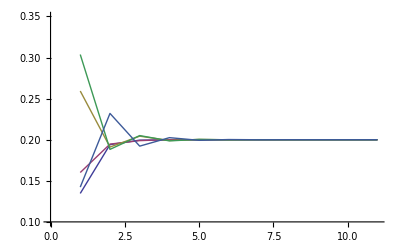

```mathematica
P[n_]:=Transpose[MatrixPower[Subscript[𝕊, 1],n].Subscript[p, 0]]⟦1⟧

MovingElement[k_]:=Table[P[n]⟦k⟧,{n,0,10}]

ListLinePlot[{MovingElement[1],MovingElement[2],MovingElement[3],MovingElement[4],MovingElement[5]},PlotRange->{.1,.35}]
```

```mathematica
Table[Chop[MatrixForm[MatrixPower[Subscript[𝕊, 1],-n].MatrixPower[Subscript[𝕊, 1],n]]],{n,0,15}]
```

{(1. | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0
0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 1.),(1. | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0
0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 1.),(1. | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0
0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 1.),(1. | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0
0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 1.),(1. | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0
0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 1.),(1. | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0
0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 1.),(1. | 0 | 2.89939×10^-10 | 1.28731×10^-10 | 0
3.54657×10^-10 | 1. | 7.96037×10^-10 | 7.25688×10^-10 | 1.23787×10^-9
0 | -3.12915×10^-10 | 1. | -2.30911×10^-10 | -3.75755×10^-10
2.7275×10^-10 | 5.4917×10^-10 | 3.25936×10^-10 | 1. | 5.68042×10^-10
0 | 0 | 0 | 0 | 1.),(1. | -3.73132×10^-9 | -2.6474×10^-9 | -5.19879×10^-9 | -4.02678×10^-10
1.37938×10^-9 | 1. | 2.94161×10^-9 | 3.59066×10^-9 | 7.12665×10^-9
7.55175×10^-10 | -3.14343×10^-9 | 1. | -3.74945×10^-9 | -1.93761×10^-10
-7.15064×10^-9 | -3.63755×10^-9 | -4.74224×10^-9 | 1. | -7.46849×10^-9
-4.41858×10^-10 | -3.72325×10^-10 | -6.20466×10^-10 | -5.12947×10^-10 | 1.),(1. | 1.36884×10^-7 | 4.00863×10^-7 | 1.83024×10^-7 | 1.11837×10^-7
-4.95687×10^-7 | 1. | -3.89696×10^-7 | -1.55372×10^-7 | -3.4342×10^-7
3.45406×10^-8 | 2.37479×10^-10 | 1. | 3.83222×10^-8 | 3.82378×10^-8
-7.4962×10^-8 | -3.38831×10^-8 | -6.10189×10^-8 | 1. | -5.82634×10^-9
-8.49566×10^-9 | -1.64899×10^-8 | 1.12451×10^-9 | -1.20507×10^-8 | 1.),(0.999994 | -1.57124×10^-6 | -6.29671×10^-6 | -4.74526×10^-6 | -0.0000106121
5.99089×10^-6 | 1. | 5.29737×10^-6 | 4.34513×10^-6 | 6.99812×10^-6
-1.08779×10^-6 | -4.31965×10^-8 | 0.999998 | -2.0139×10^-6 | -2.74101×10^-6
2.00817×10^-6 | 1.06611×10^-6 | 2.48533×10^-6 | 1. | 3.31687×10^-6
4.37202×10^-8 | 1.6671×10^-7 | 1.40508×10^-7 | -7.06713×10^-8 | 1.),(0.999999 | 9.35293×10^-6 | 0.0000182263 | 0.0000642102 | -1.96539×10^-6
0.0000206143 | 0.999982 | -0.0000447652 | -0.0000557047 | -0.0000510779
7.60091×10^-7 | 0.0000142163 | 1.00001 | 0.0000326434 | 0.0000117803
0.0000249718 | 0.0000263068 | 0.0000246219 | 1.00001 | 0.0000286079
2.33986×10^-6 | 7.29378×10^-7 | 1.28831×10^-6 | 6.69625×10^-6 | 1.),(0.998949 | -0.00230004 | 0.000100576 | -0.000878202 | -0.000242451
-0.00210213 | 0.998812 | -0.002439 | -0.00158638 | -0.00236313
-0.000365234 | -0.0000234841 | 1.00034 | 0.000055498 | 0.000096619
-0.000129897 | 0.000231813 | -0.000197836 | 0.999992 | 0.000035723
0.000199415 | 0.000116504 | 0.000245696 | 0.000193414 | 1.00021),(1.00785 | -0.000113084 | 0.0174642 | -0.00622087 | 0.00863845
0.0296178 | 1.04989 | 0.00652834 | 0.0279065 | 0.00428244
0.00337287 | -0.000875234 | 1.01257 | 0.00558707 | 0.00781464
0.00671914 | 0.0113489 | -0.00227586 | 1.0066 | -0.00108074
-0.00372745 | -0.00469475 | -0.00278393 | -0.00407957 | 0.996715),(1.5928 | 0.382543 | 0.437287 | 0.534691 | 0.16034
0.0930818 | 0.673441 | -0.385461 | -0.138344 | 0.205601
-0.315405 | -0.203741 | 0.758383 | -0.153093 | -0.370817
0.0993935 | -0.0270936 | 0.0215248 | 0.969697 | 0.184228
-0.0206509 | -0.0126494 | -0.00556226 | -0.011779 | 0.971038),(7.20446 | -3.90527 | -2.25946 | 1.85094 | 4.3781
-21.7799 | -6.77602 | -11.1656 | -17.3374 | -18.5376
-0.117979 | -2.36274 | -1.43119 | -1.33155 | -1.90769
-6.15157 | -4.15728 | -3.67295 | -4.94591 | -6.16365
0.313738 | -0.361201 | -0.361458 | -0.0642416 | 1.02774),(-191.573 | -72.4027 | -74.1248 | -113.851 | 3.47603
141.864 | 20.5992 | 153.142 | 152.032 | 114.527
39.247 | 57.9991 | 39.4861 | 25.0526 | 59.1029
156.404 | 113.439 | 155.487 | 131.077 | 130.82
-2.54092 | -1.23403 | -3.08997 | 2.58982 | -0.0253798)}

```mathematica
MatrixPower[Subscript[𝕊, 1],12]//MatrixForm
```

(0.2 | 0.2 | 0.2 | 0.2 | 0.2
0.2 | 0.2 | 0.2 | 0.2 | 0.2
0.2 | 0.2 | 0.2 | 0.2 | 0.2
0.2 | 0.2 | 0.2 | 0.2 | 0.2
0.2 | 0.2 | 0.2 | 0.2 | 0.2)

```mathematica
Det[%]//Chop
```

0

```mathematica
Inverse[Subscript[𝕊, 1]]//MatrixForm
```

(-5.4472 | 11.1276 | -3.94095 | 1.14369 | -1.88313
11.1276 | -5.66005 | 2.01134 | -5.06613 | -1.41275
-3.94095 | 2.01134 | 1.60923 | -0.423318 | 1.7437
1.14369 | -5.06613 | -0.423318 | 2.08784 | 3.25792
-1.88313 | -1.41275 | 1.7437 | 3.25792 | -0.705734)

```mathematica
Inverse[Subscript[𝕊, 1]]
```

{{-5.4472,11.1276,-3.94095,1.14369,-1.88313},{11.1276,-5.66005,2.01134,-5.06613,-1.41275},{-3.94095,2.01134,1.60923,-0.423318,1.7437},{1.14369,-5.06613,-0.423318,2.08784,3.25792},{-1.88313,-1.41275,1.7437,3.25792,-0.705734}}

```mathematica
Table[Total[Inverse[Subscript[𝕊, 1]]⟦k⟧],{k,1,5}]
```

{1.,1.,1.,1.,1.}